### 2

#### a

```mathematica
Integrate[2/9(x+1)(2-x),{x,-1,y}]
```

```mathematica
7/27+(4 y)/9+y^2/9-(2 y^3)/27
Simplify[7/27+(4 y)/9+y^2/9-(2 y^3)/27]
```

7/27+(4 y)/9+y^2/9-(2 y^3)/27

-1/27 (1+y)^2 (-7+2 y)

#### b

```mathematica
Integrate[2/9(x+1)(2-x),{x,-1,9/5}]
```

3332/3375

```mathematica
N[3332/3375]
```

0.987259

#### c

```mathematica
Integrate[2/9(x+1)(2-x)*x,{x,-1,2}]
```

1/2

#### d

```mathematica
Integrate[Exp[t*x]*2/9(x-1)(2-x),{x,-1,2}]
```

```mathematica
(2 ⅇ^-t (2+ⅇ^(3 t) (-2+t)+5 t+6 t^2))/(9 t^3)
```

(2 ⅇ^-t (2+ⅇ^(3 t) (-2+t)+5 t+6 t^2))/(9 t^3)

#### e

```mathematica
D[(2 ⅇ^-t (2+ⅇ^(3 t) (-2+t)+5 t+6 t^2))/(9 t^3),{t,3}]
```

(2 ⅇ^-t (5+ⅇ^(3 t)+3 ⅇ^(3 t) (-2+t)+12 t))/(9 t^3)-(2 ⅇ^-t (2+ⅇ^(3 t) (-2+t)+5 t+6 t^2))/(3 t^4)-(2 ⅇ^-t (2+ⅇ^(3 t) (-2+t)+5 t+6 t^2))/(9 t^3)

```mathematica
fm3[t_] := (
D[(2 ⅇ^-t (2+ⅇ^(3 t) (-2+t)+5 t+6 t^2))/(9 t^3),{t,3}]
)
```

```mathematica
fm1[t_] := (
D[(2 ⅇ^-t (2+ⅇ^(3 t) (-2+t)+5 t+6 t^2))/(9 t^3),{t,1}]
)
```

```mathematica
Limit[ fm1[t], t->0]
```

1/2

```mathematica
Limit[fm3[t], t-> 0]
```

2/5

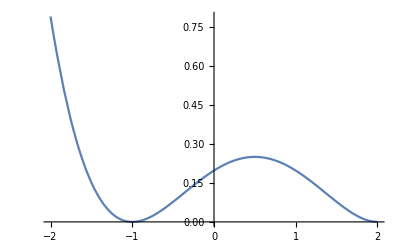

```mathematica
Plot[(2/9(x+1)(2-x))^2, {x,-2,2}]
```

```mathematica
Integrate[(2/9(x+1)(2-x))^2, {x,-1,2}]
```

2/5

#### f)

```mathematica
Integrate[2/9(x+1)(2-x),{x,-Sqrt[y],Sqrt[y]}]
```

```mathematica
(8 √y)/9-(4 y^(3/2))/27
Simplify[(8 √y)/9-(4 y^(3/2))/27]
```

(8 √y)/9-(4 y^(3/2))/27

-4/27 (-6+y) √y

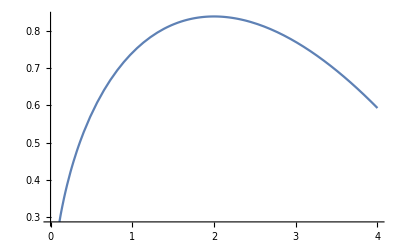

```mathematica
Plot[-4/27 (y-6) √y,{y,0,4}]
```

```mathematica
Limit[1/27 (-2 y^(3/2)+3 y+12 √y), y-> 1]
```

13/27

```mathematica
D[Sqrt[y],{y}]
```

1/(2 √y)

```mathematica
Simplify[2/9 ((-Sqrt[y]) + 1) (2 - (-Sqrt[y]))*Abs[-1/(2Sqrt[y])]+2/9 ((Sqrt[y]) + 1) (2 - Sqrt[y])*Abs[1/(2Sqrt[y])]]
```

-(2 (-2+y))/(9 √Abs[y])

```mathematica
Simplify[2/9 ((Sqrt[y]) + 1) (2 - Sqrt[y])*Abs[1/(2Sqrt[y])]]
```

(2+√y-y)/(9 √Abs[y])

```mathematica
Integrate[-(2 (y-2))/(9 √y),{y,0,1}]
```

20/27

```mathematica
Integrate[-((√y-2) (√y+1))/(9 √y), {y,1,4}]
```

7/27

```mathematica
fpdf2=ProbabilityDistribution[2/9(x+1)(2-x),{x,-1,2}]
```

ProbabilityDistribution[2/9 (2-x) (1+x),{x,-1,2}]

```mathematica
fpdf2[1]
```

ProbabilityDistribution[2/9 (2-x) (1+x),{x,-1,2}][1]

```mathematica
TransformedDistribution[x^2, x\[Distributed] fpdf2]
```

TransformedDistribution[x^2,x\[Distributed]fpdf2]

```mathematica
PDF[TransformedDistribution[x^2, x\[Distributed] fpdf2],x]
```

```mathematica
Piecewise[{{(2+√x-x)/(9 √x), 1≤x<4}, {-(2 (-2+x))/(9 √x), 0<x<1}, {0, x≥4||x<0}, {Indeterminate, True}}]
```

```mathematica
Remove[x]
```